Universidad de Jaén. Escuela Politécnica Superior de Jaén.
Grado en Ingeniería Informática           
Asignatura: Análisis y Métodos Numéricos. Curso 2024/25
F.Javier Muñoz Delgado

# TEMA 4. FUNCIONES REALES. NOTAS Y PRÁCTICAS.

## Contenidos

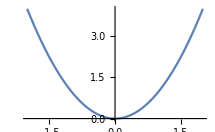
Este tema es básicamente conocido por quienes hayan cursado Bachillerato.
Una función real de variable real es una aplicación  f:D⊂ℝ⟶ℝ que asigna a cada número real, x, del dominio D, otro valor real, f(x). 

Usualmente se facilita un fórmula para conocer el valor asociado a cada número. Por ejemplo, es fácil encontrarnos con expresiones como f(x) = x^2. En esas circunstancias, debemos entender que el dominio es el conjunto de números reales donde tiene sentido la expresión matemática. Es decir, el dominio, en lugar de ser algo dado, es algo que debe ser “calculado”.

La gráfica de una función es el conjunto de puntos {(x,f(x)), con x en el dominio de f}. Suele aparecer como una línea en el plano y nos facilita comprender con una imagen el comportamiento de la función.
						-Graphics-

El problema de la existencia y cálculo del límite de una función puede plantearse en puntos donde haya puntos del dominio (diferentes al punto en cuestión) tan cercanos como deseemos. 
(Matemáticamente, para hablar de límite de la función f en el punto x_0, es necesario que en cualquier intervalo de la forma (x_0-δ,x_0+δ), para cualquier δ>0, haya puntos del dominio de f distintos del x_0) 

Así nos podemos plantear el problema del límite de la función √x  o de log(x) en el punto 0, esté o no definida la función en el 0. Lo importante es poder evaluar la función en puntos cercanos al 0. En cambio, no tendría sentido plantearse el problema del límite de estas funciones en el punto -2.
El límite sería el valor “esperado” de una función en un punto, independientemente de que la función esté definida o no en ese punto, o del valor que la función pudiese tomar en ese punto. “Esperado” según los valores de f en los puntos cercanos.
(Matemáticamente, existe el límite de la función f(x) en el punto x_0, si existe un número real L que cumple que para cada ϵ>0 existe un número δ>0, dependiente de ϵ, tal que si |x-x_0|<δ, x≠x_0, x∈D, |f(x)-L|<ϵ.

El valor L, sería el límite de f(x) en el punto x_0 y escribiríamos lim_(x→x_0) f(x)=L)

Como ocurría con las sucesiones, la definición de límite, no suele ser muy útil a la hora de calcular límites. Su interés, además de por ser necesario tener una definición, es para demostrar propiedades de los límites que sí serán de utilidad para el cálculo de límites.

También puede hablarse de límite en más o menos infinito, si podemos evaluar la función “cerca” de más o de menos infinito, es decir, si el dominio de la función no está acotado superior o inferiormente, respectivamente.

Las funciones continuas son las que en cada punto de su dominio coincide el valor de la función con el valor del límite en dicho punto.
(Escribiríamos lim_(x→x_0) f(x)=f(x_0) en todos los puntos del dominio.)

La mayoría de las funciones que usamos son continuas (polinomios, exponencial, logaritmo, raíz cuadrada, seno, coseno, ...). Además, la suma, la resta, el producto, el cociente y la composición de funciones continuas es de nuevo una función continua en el dominio que resulte. Por ejemplo, la función f(x)=1/x es una función continua en todos los puntos de su dominio, pues es el cociente de dos funciones continuas. En el punto 0 no podemos decir que f sea continua, ni no continua, simplemente no hay función en el punto 0.

Si bien la definición de continuidad, ligada a la definición de límite, nos lleva a pensar en lo difícil que es probar la continuidad de una función, el hecho de que las funciones usuales, y muchas de las que podemos generar, sean continuas, nos facilita las cosas. De hecho, en cursos anteriores, las funciones para estudiar la continuidad (también la derivabilidad) se limitaban prácticamente a las funciones definidas a trozos, pues no es fácil encontrar de otro modo funciones no continuas. 

Gracias a la continuidad, el problema de la existencia y del cálculo del límite de una función puede simplificarse en la mayoría de los puntos (todos los del dominio). El problema se reduciría a límites en más o menos infinito, o en puntos fuera del dominio, pero “pegando” (por ejemplo, en el 0 si el dominio fuese (0,∞) ). 

Además de la continuidad, las propiedades de los límites respecto a la suma, resta, producto, cociente, producto por un número, potencias o composición con funciones continuas puede simplificar mucho los cálculos.

Una función tiene asíntota horizontal hacia más infinito, si el límite de la función hacia más infinito es un número real. También puede haber hacia menos infinito (y podría ser diferente a la de más infinito). Una función f tiene asíntota oblicua y=ax+b hacia más infinito si el límite de f(x)-(ax+b) es 0 cuando x tiende hacia menos infinito. De forma análoga se define una asíntota oblicua hacia menos infinito.  

Las funciones pueden tener comportamientos diferentes hacia más y menos infinito. Pueden aparecer diferentes asíntotas horizontales u oblicuas. ATENCIÓN: aunque en las funciones racionales aparece un mismo comportamiento, en general esto no ocurre y una función podría tener dos asíntotas horizontales diferentes o una horizontal y otra oblicua, o dos oblicuas diferentes, etc.

Teorema de Bolzano. Si f es una función continua en un intervalo [a,b] y toma valores de diferente signos en los extremos (es decir, f(a)*f(b)<0) entonces existe un valor c, a<c<b, con f(c)=0.
Para encontrar ese punto c, aunque sea de forma aproximada, podemos dividir sucesivamente el intervalo [a,b] considerando el punto medio y quedándonos con el subintervalo donde aparezca el cambio de signo. Se trata del método de bisección. Es un método para aproximar soluciones de la ecuación f(x)=0. Se estudiarán más métodos en la segunda parte de la asignatura. 

Teorema de Weierstrass. Si f es una función continua en un intervalo [a,b], la función alcanza su máximo y su mínimo absoluto en el intervalo [a,b]. Es decir, existe unos puntos c y d en [a,b] donde m=f(c)≤f(x)≤f(d)=M para cualquier x en [a,b]. M será el valor máximo absoluto de f y m el valor mínimo absoluto de f.

## Trabajando con el Mathematica

## Definición de una función. Función definida a trozos. Dibujar la gráfica de una función. Cálculo de límites (en un punto, en el infinito, laterales) Estudio del signo de una función Modificaciones de una gráfica (simetrías respecto a ejes verticales u horizontales, “comprimir” o “expandir”) Encontrar una función periódica

Para definir una función consideramos un nombre (que el Mathematica no haya utilizado) que puede ser una o varias letras y puede también tener números (se distingue entre mayúsculas y minúsculas). El nombre que escojamos debería aparecer en azul, si el Mathematica no lo tiene, y al definir la función (pulsar Intro) debe pasar a negro.

```mathematica
f[x_]:= Sin[x]
```

Una vez definida la función, puede evaluarse la función escribiendo

```mathematica
f[0]
```

0

También podemos evaluar la función en varios puntos formando una lista (escribiendo entre llaves y separando por comas).

```mathematica
{f[0],f[1],f[2],f[3],f[4]}
```

{0,Sin[1],Sin[2],Sin[3],Sin[4]}

Si queremos tener una aproximación numérica decimal.

```mathematica
{f[0],f[1],f[2],f[3],f[4]}//N
```

{0.,0.841471,0.909297,0.14112,-0.756802}

```mathematica
N[{f[0],f[1],f[2],f[3],f[4]},20]
```

{0,0.84147098480789650665,0.9092974268256816954,0.1411200080598672221,-0.75680249530792825137}

Para funciones definidas a trozos, utilizamos la instrucción Which. Escribimos una condición y a continuación el valor de la función en ese caso. Sucesivamente, escribimos tantas condiciones y definiciones, como correspondan.

```mathematica
g[x_]:=Which[x≤3, x-2, 3<x<6, 2x+1, 6≤x, x^2/(3x+1)]
```

En ocasiones, para la última condición puede ser útil usar True, que siempre será cierta y la función tomará el valor que indiquemos para el resto de puntos donde no se cumplan las condiciones anteriores.

Si cambiamos la definición de f puede ser interesante “limpiar” de la memoria la definición de f. Para ello usamos la función Clear

```mathematica
Clear[f]
```

Para dibujar la gráfica de una función utilizamos la instrucción Plot. Debemos precisar un intervalo.

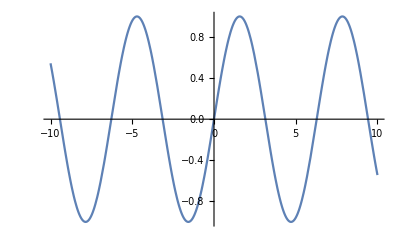

```mathematica
Plot[f[x],{x,-10,10}]
```

La gráfica aparece en la proporción áurea. Si queremos cambiar la proporción, o queremos que la escala sea la misma en los dos ejes, podemos utilizar la función AspectRatio añadiendo un número (que sería la proporción entre alto y ancho) o Automatic (si queremos que la escala sea la misma).

```mathematica
Plot[f[x],{x,-10,10}, AspectRatio->2]
```

-Graphics-

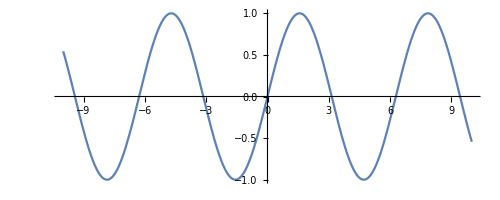

```mathematica
Plot[f[x],{x,-10,10}, AspectRatio->Automatic]
```

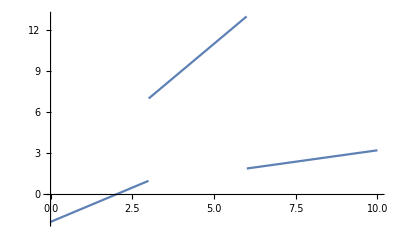

```mathematica
Plot[g[x],{x,0,10}]
```

También se pueden dibujar varias gráficas:

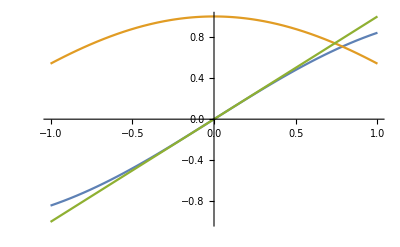

```mathematica
Plot[{Sin[x],Cos[x],x},{x,-1,1}]
```

## Límites. Asíntotas horizontales y oblicuas.

Para calcular límites, podemos utilizar la función Limit. Podemos calcular el límite en un punto, límites laterales y límites en el infinito.

#### Ejemplo 1

```mathematica
Limit[(x^2-4)/(x-2), x->2]
```

4

Para escribir la flecha podemos utilizar la paleta (en la fila del 1, 2 y 3) o escribir el signo menos (-) y el signo mayor (>), al seguir escribiendo, los símbolos se combinan y forman la flecha.

Para hacer este límite a mano (cociente de polinomios):
Observamos que se trata de un cociente de dos polinomios que se anulan en el 2. Por ello, nos encontramos con una indeterminación, un 0/0. 

Los polinomios tienen una propiedad muy exclusiva. Si un polinomio p(x) cumple que p(a)=0 en un punto a, entonces podemos escribir p(x)=(x-a) q(x), donde q(x) es un polinomio de un grado menos que el de p(x). Para encontrar q(x) podemos dividir como una división normal o usando el algoritmo de Ruffini.
 
Al escribir el numerador como el producto (x-2)(x+2), podemos simplificar, (x^2-4)/(x-2)= ((x-2)(x+2))/(x-2)= x+2. Así, es fácil ver que el límite va a ser 4.

#### Ejemplo 2.

```mathematica
Limit[Sin[x]/x, x->0]
```

1

Para hacer este límite a mano, observamos que se trata de un cociente de dos funciones que se anulan en el punto 0 (es de nuevo una indeterminación). 

En este caso, como no son polinomios no podemos simplificar como en el ejemplo anterior. Habría que estudiar cómo se acercan a 0 numerador y denominador. Cuando estudiemos derivadas, podremos utilizar la regla de L’Hôpital, y tendremos que el límite de Sin[x]/x será el mismo (en caso de existir) que el de Cos[x]/1. Este cociente tiende a 1 cuando x tiende a cero. Por tanto, el límite pedido existe y es también 1. Se trata de la versión para funciones del Criterio de Stolz que estudiamos para sucesiones. Allí, también para estudiar sucesiones con un cociente que nos llevaba a una indeterminación estudiábamos el crecimiento de numerador y denominador, no derivando, sino calculando la diferencia entre un término y el anterior.

#### Ejemplo 3.

```mathematica
Limit[(1-√x)/(1-x), x->1]
```

1/2

Para hacer este límite a mano (diferencia de raíces):
Dado que nos encontramos con otra indeterminación 0/0, podríamos multiplicar y dividir por 1+√x
y obtendríamos 
		(1-√x)/(1-x)(1+√x)/(1+√x)= (1-x)/((1-x) (1+√x))= 1/(1+√x)
que tiende a 1/2 cuando x tiende a 1.

#### Ejemplo 4.

También podemos calcular límites en infinito. El símbolo de infinito ∞ se encuentra en la paleta en la fila de las cifras 1, 2, 3. También puede escribirse Infinity.

```mathematica
Limit[(x^2+3)/(x^2+1), x->∞]
```

1

```mathematica
Limit[(x^2+3)/(x^2+1), x->-Infinity]
```

1

Para hacer este límite a mano (cociente de polinomios, en el infinito):
Dado que nos encontramos con una indeterminación ∞/∞, podríamos dividir numerador y denominador por una potencia adecuada. En este caso, x^2  y obtendríamos 
		(x^2+3)/(x^2+1)= (1+3/x^2)/(1+1/x^2)
que tiende a 1/1 cuando x tiende a ∞.

#### Ejemplo 5.

Para calcular límites laterales, debemos especificar la dirección para acercarse al punto.

```mathematica
Limit[g[x],x->3, Direction->1]
```

1

```mathematica
Limit[g[x],x->3, Direction->-1]
```

7

Direction → 1 significa que la variable debe acercarse creciendo hacia el punto del límite (por la izquierda). Direction → -1 sería acercarse decreciendo (por la derecha). 

El límite de g(x) en el punto 3, con x creciente (sería por la izquierda) es 1 (la función vale en ese caso x-2) y con x decreciente (sería por la derecha) es 7 (la función vale 2x+1). Significa que no hay límite en el punto 3, sólo límites laterales. Si pedimos el límite, nos indica que no hay límite.

```mathematica
Limit[g[x],x->3]
```

Indeterminate

#### Ejemplo 6.

Otro ejemplo de límite que no existe, ni siquiera los laterales:

```mathematica
Limit[Cos[1/x],x->0]
```

Indeterminate

```mathematica
Limit[Cos[1/x],x->0, Direction->1]
```

Indeterminate

```mathematica
Limit[Cos[1/x],x->0, Direction->-1]
```

Indeterminate

Observamos su gráfica.

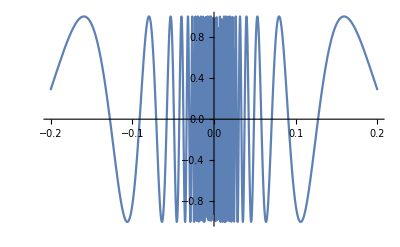

```mathematica
Plot[Cos[1/x],{x,-0.2,0.2}]
```

#### Ejemplo 7.

En cambio, sí existe el límite:

```mathematica
Limit[x Cos[1/x],x->0]
```

0

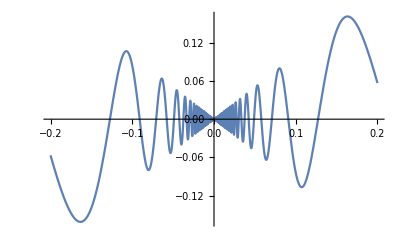

```mathematica
Plot[x Cos[1/x],{x,-0.2,0.2}]
```

Se trata del producto de una función que tiende a 0 (la función x) con otra que no tiene límite, pero está acotada (la función cos(1/x) toma valores entre -1 y 1).

Sabemos que cuando existe el límite de dos funciones en un punto, el producto de ambas también tiene límite, y el límite es el producto de los límites. Además de esta propiedad para el producto, tenemos que si multiplicamos dos funciones, una que tiende a cero en un punto y otra que está acotada en un entorno de dicho punto, el producto tiene límite y también vale 0.

#### Ejemplo 8.

Las funciones pueden tener diferente comportamiento hacia más o menos infinito. Pueden tener diferentes tipos de asíntotas (horizontal y oblicua), o siendo del mismo tipo, que sean diferentes (dos horizontales distintas, o dos oblicuas distintas).

La función ⅇ^x/(1+ⅇ^x) tiene un comportamiento diferente en ∞ y -∞. Tendría dos asíntotas horizontales diferentes: y=0 e y=1.

```mathematica
Limit[ⅇ^x/(1+ⅇ^x), x-> ∞]
```

1

```mathematica
Limit[ⅇ^x/(1+ⅇ^x), x-> -∞]
```

0

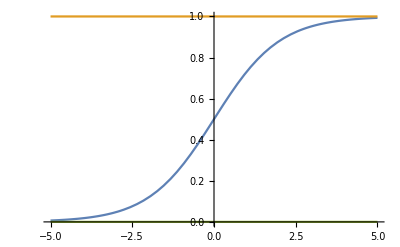

```mathematica
Plot[{ⅇ^x/(1+ⅇ^x),1,0},{x,-5,5}]
```

#### Ejemplo 9.

La función (x ⅇ^x)/(1+ⅇ^x) tiene un comportamiento diferente en ∞ y -∞. Tendría una asíntota oblicua (y=x) y otra horizontal (y=0).

```mathematica
Limit[(x ⅇ^x)/(1+ⅇ^x), x-> ∞]
```

∞

```mathematica
Limit[(x ⅇ^x)/(1+ⅇ^x)-x, x-> ∞]
```

0

```mathematica
Limit[(x ⅇ^x)/(1+ⅇ^x), x-> -∞]
```

0

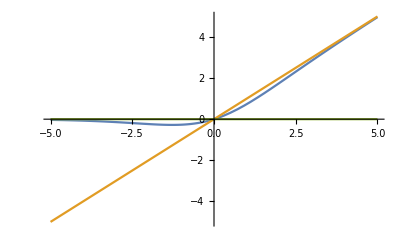

```mathematica
Plot[{(x ⅇ^x)/(1+ⅇ^x),x,0},{x,-5,5}]
```

#### Ejemplo 10.

La función valor absoluto de x tiene también un comportamiento diferente en ∞ y -∞. Tiene dos asíntotas oblicuas (y=x e y=-x).

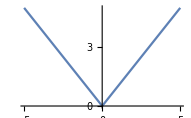

```mathematica
Plot[Abs[x],{x,-5,5}]
```

Si le sumamos x a la función valor absoluto de x tiene también un comportamiento diferente en ∞ y -∞. Tiene una asíntota horizontal y=0, y otra oblicua y=2x.

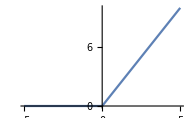

```mathematica
Plot[x+Abs[x],{x,-5,5}]
```

Las funciones racionales, cociente de dos polinomios, tienen el mismo comportamiento hacia infinito y menos infinito, pero esto no tiene por qué suceder con otras funciones.

Si una función es el cociente de dos polinomios p(x)/q(x), podemos distinguir los siguientes casos:
a) Si el grado de q(x) es mayor que el grado de p(x), nos encontramos con una asíntota horizontal y=0 tanto hacia ∞, como hacia -∞.
b) Si el grado es menor o igual, si realizamos la división obtendremos un cociente y un resto, y podremos escribir p(x)/q(x) = c(x) + r(x)/q(x). 
	b.1) Si el cociente, c(x), fuese una constante, tendremos una asíntota horizontal y=c, tanto hacia ∞, como hacia -∞, pues r(x)/q(x) tiende a cero, tanto en infinito, como en menos infinito.
	b.2) Si el cociente es un polinomio de grado 1, nos encontraremos con una asíntota oblicua y=c(x), tanto hacia ∞, como hacia -∞. Pues, como decíamos antes, r(x)/q(x) tenderá hacia cero.
	b.3) Si el grado de c(x) es mayor que uno entonces no tendremos asíntotas, ni horizontal, ni oblicua.

## Signo de una función

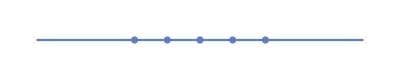
Para diferentes problemas, debemos encontrar el signo de una función. Para estudiar el crecimiento de una función, solemos considerar la derivada de la función y estudiar su signo. Para el estudio de la convexidad, hacemos lo mismo con la segunda derivada.

Empecemos recordando el Teorema de Bolzano:
Teorema: Si f es una función continua en un intervalo [a,b] con cambio de signo en los extremos, f(a)f(b)<0, entonces existe un punto c entre a y b, donde f(c)=0.

A partir del teorema de Bolzano tenemos que:

Si tenemos una función continua definida en un intervalo (a,b) (puede ser abierto o cerrado en los extremos) y la función no se anula en ningún punto del intervalo, entonces la función es siempre positiva o siempre negativa en el intervalo. 
(Si la función fuese mayor que cero en un punto del intervalo y en otro menor que cero, el teorema de Bolzano nos diría que entre esos dos puntos la función tendría que valer cero en algún punto. Pero como la función no se anula nunca en el intervalo, esto nos indica que la función no cambia de signo.)

Gracias a esto podemos dar el procedimiento para estudiar los signos de una función:

1) Estudiar el dominio de la función.
2) Estudiar dónde la función es continua.
3) Estudiar dónde se anula la función.
4) Formamos los intervalos dados por los puntos anteriores y evaluamos.

Ejemplo: Estudiemos el signo de la función f(x) = (x^2- 4)/(x^4-x^2).

1)  Estudiamos el dominio de la función. El dominio podría haber sido indicado al definir la función. Como no lo han dado, se entiende que es donde la expresión matemática tenga sentido.
Dado que tenemos dos polinomios, sabemos que están definidos en todo ℝ. El problema viene porque tenemos una división, que puede realizarse salvo que el denominador valga 0. Estudiemos si el denominador se anula:
(x^4-x^2)=x^2(x^2-1)=0 ⟹ x^2=0 ó (x^2-1)=0  ⟹  x=0, x=1 ó x=-1.
Por tanto, el domino es ℝ - {-1, 0, 1}.

2) Estudiemos la continuidad. La función es continua en todo el dominio, por ser el cociente de polinomios, que son funciones continuas. 
Por tanto, la función es continua en ℝ - {-1, 0, 1}.
(En la mayoría de las ocasiones nos vamos a encontrar con funciones continuas, sin embargo con frecuencia nos encontramos con funciones definidas a trozos, en las cuales vemos cómo al pasar de un trozo a otro la continuidad se puede perder.) 

3) Estudiemos cuándo se anula la función. Como es un cociente, estudiamos cuándo se anula el numerador. 
(x^2- 4)=0 ⟹ x^2= 4 ⟹ x=2 ó x=-2. La función se anula en {-2, 2}.

4) Ahora consideramos toda la recta real y marcamos el dominio, las discontinuidades y los ceros de la función.

-Graphics-
Los intervalos de signos serán (-∞, -2), (-2,-1), (-1, 0), (0,1), (1,2), (2, ∞). En cada uno de estos intervalos la función tiene un solo signo. Basta ahora evaluar la función en un punto de cada uno de ellos.
f(-3)=5/72, f(-3/2)=-28/45, f(-1/2)=20, f(1/2)=20, f(3/2)=-28/45, f(3)=5/72.

Por tanto, f es positiva en   (-∞, -2), (-1, 0), (0,1) y (2, ∞) y es negativa en (-2,-1) y (1,2). Se anula en los puntos -2 y 2.

Los cálculos con el Mathematica serían:

```mathematica
Solve[x^4-x^2==0,x]
```

{{x→-1},{x→0},{x→0},{x→1}}

```mathematica
Solve[x^2-4==0,x]
```

{{x→-2},{x→2}}

```mathematica
h[x_]:= (x^2-4)/(x^4-x^2)
```

```mathematica
{h[-3],h[-1.5],h[-0.5],h[0.5],h[1.5],h[3]}//N
```

{0.0694444,-0.622222,20.,20.,-0.622222,0.0694444}

También podríamos haber esbozado la gráfica de la función. Para ello tenemos en cuenta:
1) La función es un cociente de polinomios. El numerador tiene grado 2 y el denominador grado 4. La función al acercarse a infinito o menos infinito, se comportaría como x^2/x^4, es decir, como 1/x^2. Por tanto nos encontramos con una asíntota horizontal y=0. Además, el cociente es positivo tanto hacia más infinito, como hacia menos infinito. Es decir, la gráfica de la función estará por encima de 0, por encima de la asíntota.

2) Los puntos que no estaban en el dominio, por anularse el denominador, podrían indicar asíntotas verticales. 
Efectivamente, cuando x se acerca a los puntos -2, 0 ó 2, el denominador se acerca a cero mientras el numerador se acerca a un valor real. La función tiene asíntotas verticales en -2, 0 y 2. Sin embargo, estas tres asíntotas tienen un comportamiento diferente. El denominador es  (x^4-x^2)=(x-0)^2(x-1)(x+1). Mientras al pasar de antes del 1 a después del 1, el polinomio cambia de signo, al pasar de antes del 0 a después del cero, el polinomio no lo hace pues (x-0) está elevado al cuadrado. También hay cambio de signo entre antes del -1 y después del -1.
Hay tres asíntotas verticales, dos son impares (x=-1, x=1) y una par (x=0). En las asíntotas pares la función tiende a más infinito por ambos lados o tiende a menos infinito por ambos lados. En las asíntotas impares, si a un lado la función tiende a menos infinito, en el otro tiende a más infinito. 

3) La función se anula en los puntos -2 y 2. El numerador es (x^2- 4) =(x-2)(x+2). Hay dos ceros simples (multiplicidad uno). En esos puntos se produce un cambio de signo de la función.

Con esta información podemos comenzar el esbozo de la gráfica de la función. Hacia menos infinito, la función parte cercana a cero y va subiendo. Será positiva hasta el -2 donde la función se anula y pasa a negativa. Después la función es negativa y tendrá que buscar la asíntota vertical x=-1. A la derecha del -1, la función será positiva (es asíntota impar). Irá decreciendo y como no puede pasar a negativa, tendrá en algún momento que volver a crecer al acercarse a la asíntota vertical par x=0. Al ser par, a la derecha de x=0, la función vendrá de más infinito y como no puede anularse en (0,1), tendrá que volver hacia más infinito al acercarse al 1. Después del 1, la función vendrá de menos infinito (pues la asíntota y=1 es impar) y crecerá. Se anulará en el punto 2 y debe acercarse a cero (asíntota horizontal y=0) aunque positiva. 

Al dibujar la gráfica de la función con el Mathematica encontramos:

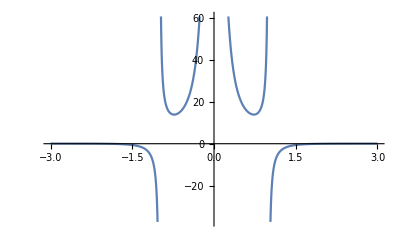

```mathematica
Plot[(x^2-4)/(x^4-x^2), {x,-3,3}]
```

Usando el Mathematica podemos ver trozos más amplios o más reducidos.

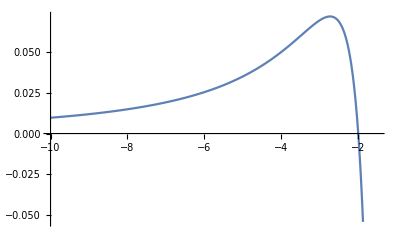
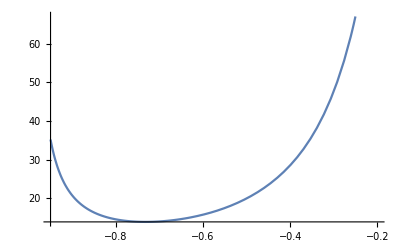
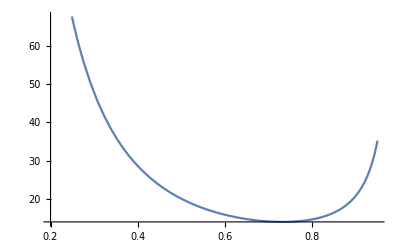
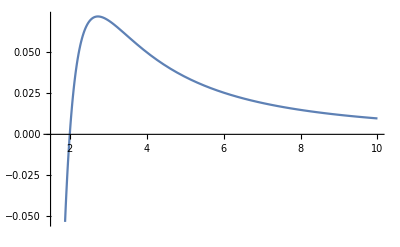

```mathematica
{Plot[(x^2-4)/(x^4-x^2), {x,-10,-1.5}], Plot[(x^2-4)/(x^4-x^2), {x,-0.95,-0.2}], Plot[(x^2-4)/(x^4-x^2), {x,0.2,0.95}], Plot[(x^2-4)/(x^4-x^2), {x,1.5,10}]}
```

Al ver la gráfica, confirmamos mucho del comportamiento de la función que habíamos previsto.

Cuando tengamos la herramienta de la derivada podemos conocer más de la función: intervalos de crecimiento, de convexidad, máximos y mínimos relativos o puntos de inflexión. La mayoría de lo que va a apareciendo ya está previsto en nuestro estudio preliminar.

Con el Mathematica también podríamos hacer los cálculos con la función Reduce:

```mathematica
Reduce[h[x]<0,x]
```

-2<x<-1||1<x<2

## Modificaciones a la gráfica de una función

¿Qué tienen en común las gráficas de f(x), f(-x), -f(x), -f(-x), f(x+2), f(x)+2, f(2x), 2f(x)?

Dada una función f(x), la función f(-x) tendría una gráfica simétrica respecto del eje vertical. La nueva función vale en el -3, lo que la inicial vale en el 3. Si quisiéramos que fuese simétrica respecto a la recta x=a, la función debería ser f(2a-x).
Dada una función f(x), la función -f(x) tendría una gráfica simétrica respecto del eje horizontal. Si quisiéramos que fuese simétrica respecto a la recta y=a, la función debería ser 2a-f(x).
Dada una función f(x), -f(-x) tendría una gráfica simétrica respecto al punto (0,0). Serían dos simetrías, respecto al eje horizontal y respecto al vertical. La nueva función valdría en el -3, lo opuesto al valor de f en el 3.
Dada una función f(x), la función f(x+2) tendría una gráfica como la de f(x) desplazada dos unidades hacia la izquierda. La función f(x+2) vale en el -2, lo que f(x) vale en el 0.
Dada una función f(x), la función f(x)+2 tendría una gráfica como la de f(x) desplazada dos unidades hacia arriba. La función f(x)+2 vale 2 unidades más en cada punto.
Dada una función f(x), la función f(2x) tendría una gráfica “comprimida” en la mitad de longitud en la dirección horizontal. Presenta una variación más rápida. (Su derivada sería el “doble”.)
Dada una función f(x), la función f(x/2) tendría una gráfica “expandida” al doble de longitud en la dirección horizontal. Varía más lentamente.
Dada una función f(x), la función 2f(x) tendría una gráfica “expandida” al doble en la dirección vertical.

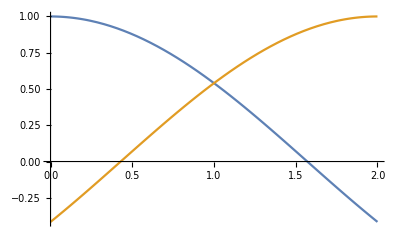

```mathematica
Plot[{Cos[x],Cos[2-x]},{x,0,2}]
```

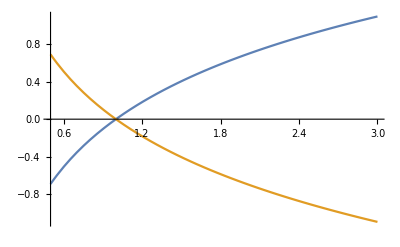

```mathematica
Plot[{Log[x],-Log[x]},{x,0.5,3}]
```

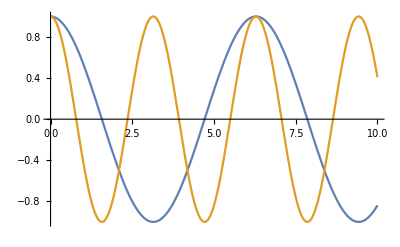

```mathematica
Plot[{Cos[x],Cos[2x]},{x,0,10}]
```

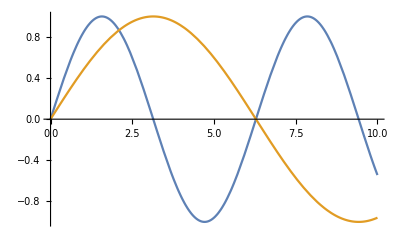

```mathematica
Plot[{Sin[x],Sin[x/2]},{x,0,10}]
```

## Encontrar una función periódica

Encontrar una función que aproxime la temperatura a lo largo del día. Supongamos que la temperatura máxima sea 31 y la mínima 15, que la función sea periódica, de período 24 y que el máximo se alcance a las 17 horas.

Las funciones seno y coseno, son funciones periódicas que oscilan entre -1 y 1.

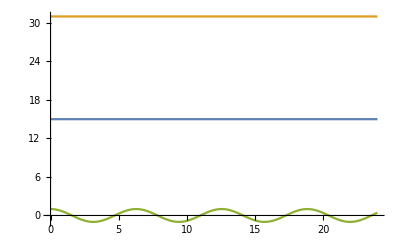

```mathematica
Plot[{15,31,Cos[x]},{x,0,24}]
```

La función que buscamos tiene un valor medio de (31+15)/2=23. Por ello podemos sumarle esta cantidad a la función coseno.

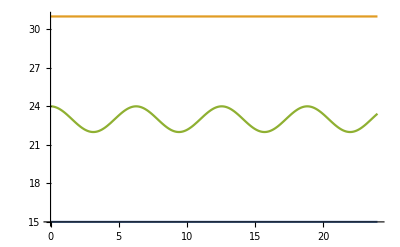

```mathematica
Plot[{15,31,23+Cos[x]},{x,0,24}]
```

El coseno tiene un máximo de 1. La función buscada tiene un máximo de 31, por ello multiplicamos la función coseno por 8, que sumado al 23, nos dará el máximo de 31.

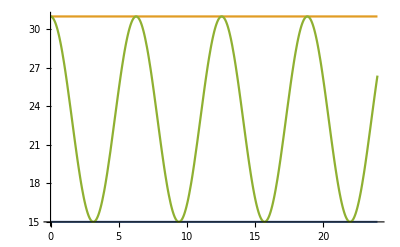

```mathematica
Plot[{15,31,23+8Cos[x]},{x,0,24}]
```

La función que buscamos debe tener un período de 24, como la función coseno tiene un período de 2π.

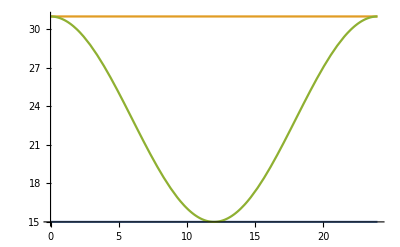

```mathematica
Plot[{15,31,23+8Cos[(2π x)/24]},{x,0,24}]
```

La función coseno tiene su máximo cuando el argumento es 0 o múltiplo de 2 π. Como queremos que el máximo de la función buscada esté en el valor 17, le restamos a x ese valor.

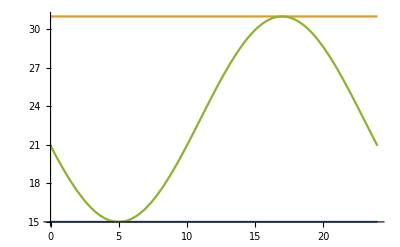

```mathematica
Plot[{15,31,23+8Cos[(2π (x-17))/24]},{x,0,24}]
```

Hemos encontrado una función que tiene los valores máximos y mínimos requeridos, que se repite cada 24 horas y que alcanza el máximo en el punto dado.
Se trata de una función del tipo A + B cos(Cx+D). 
El valor de A sube o baja la gráfica. El valor de B permite que la oscilación sea mayor o menor. El valor de C cambia el período (o la frecuencia) de la función. El valor de D hace que la gráfica se desplace a izquierda o derecha.
El máximo de la función es A+B, el mínimo de la función es A-B, el período es (2π)/C y alcanza el máximo cuando x es -D/C.
También se podría trabajar con la función seno, aunque en este caso el máximo se alcanzaría cuando el argumento sea π/2, en vez del 0, como ocurría con la función coseno.

Ejercicio. A partir de las funciones seno y coseno, encontrar una gráfica similar a la siguiente. Tratar de hacerlo primero solo con funciones senos, y luego solo con funciones cosenos.

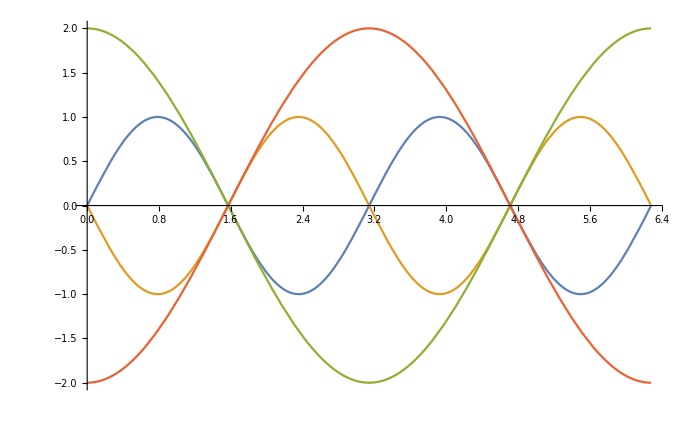

Ejercicio: Calcular el dominio de la función f(x) = Log(Log(√(1/(x+1)))).
Solución:
Dado un valor de x, la primera operación es sumar 1. El dominio de x+1 es todo ℝ.
La siguiente operación es calcular el inverso, es decir  1/(x+1). Para que pueda calcularse, es necesario que x+1 no sea cero. Por tanto, el dominio de 1/(x+1) es ℝ-{-1}.
Para calcular la raíz cuadrada, se necesita que el radicando sea mayor o igual a cero. √(1/(x+1)) se puede calcular si 1/(x+1) ≥ 0. Un cociente es positivo si numerador y denominador tienen el mismo signo, como el numerador es constante y positivo, el denominador, debe ser también mayor que cero (igual no valdría para hacer la división). Por tanto, se necesita que x+1 sea mayor que cero. El dominio de √(1/(x+1)) es (-1,∞).
Para poder calcular el logaritmo de √(1/(x+1)) es necesario que la raíz cuadrada sea mayor que cero. como el radicando es mayor que cero la raíz debe ser mayor que cero.   El dominio de Log(√(1/(x+1))) es (-1,∞).
Finalmente, para poder calcular el logaritmo de Log(√(1/(x+1))) es necesario que Log(√(1/(x+1))) sea mayor que cero, es decir que √(1/(x+1)) sea mayor que 1. Esto nos lleva a que 1/(x+1) tenga que ser, además de positivo, mayor que 1. Por tanto, x+1<1, o lo que es igual x<0. 

El dominio de Log(Log(√(1/(x+1)))) es (-1,0).
Con el Mathematica podríamos haber dibujado la gráfica de la función.

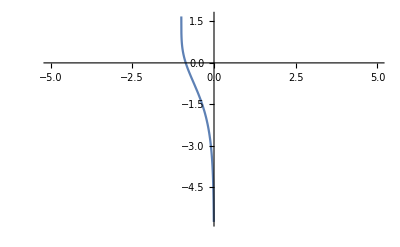

```mathematica
Plot[Log[Log[Sqrt[1/(x+1)]]],{x,-5,5}]
```

Vemos que solo hay gráfica en (-1,0). Aún mejor, podemos usar la función Reduce.

```mathematica
Reduce[Log[Sqrt[1/(x+1)]]>0,x,Reals]
```

-1<x<0